## 2 | Variational Quantum Eigensolver (VQE)

The variational quantum eigensolver (VQE) is a hybrid algorithm that combines classical and quantum computing to determine the ground state energy of a Hamiltonian. It utilizes quantum algorithms to calculate expected energy values and classical optimization techniques for minimizing that energy. VQE plays a crucial role in quantum optimization, particularly in solving complex problems in quantum chemistry and materials science. By enabling efficient simulations of intricate systems, VQE can address optimization tasks that are challenging for classical methods alone.

### Physical Background

Before understanding VQE, we need to understand what problem we are trying to solve. At its core, VQE is an algorithm designed to compute energies of quantum systems, especially molecules. To understand this, we must introduce the most important object in quantum physics: Hamiltonians.

#### What is a Hamiltonian?

In classical mechanics, the evolution of a system is determined by Newton’s laws. In quantum mechanics, the underlying physics is governed by a single mathematical object called the Hamiltonian. Intuitively, the Hamiltonian is the energy operator of a system. It contains all the physics:

Kinetic energy

Potential energy

Interactions between particles

If we know the Hamiltonian, we know the physics of the system.

Mathematically, the Hamiltonian is an operator 𝐻̂ that acts on the quantum state ψ. One of fundamental equations of quantum mechanics is the time-independent Schrödinger equation:

Ĥ ψ_E=Eψ_E

which an eigenvalue relationship with E the eigenvalue of Hamiltonian (also called eigenenergy) and ψ_E its corresponding eigenstate (aslo called eigenvector because as a math object, they are vectors). Some important physics follows this eigenvalue relationship:

The allowed energies of the system are the eigenvalues of the Hamiltonian.

The corresponding quantum states are the eigenvectors.

For VQE the main goal is:

Given a Hamiltonian, find its lowest eigenvalue (the ground-state energy).

#### Why Molecular Energies Are Hard

Suppose we want the energy of a molecule . A molecule contains a nuclei (heavy, positively charged) and electrons (light, negatively charged).

Every particle interacts with every other particle through Coulomb forces. The total energy operator of a molecule contains :

Kinetic energy of nuclei

Kinetic energy of electrons

Electron–nucleus attraction

Electron–electron repulsion

Nucleus–nucleus repulsion

Even for a small molecule, this is an enormous many-body problem. The exact molecular Schrödinger equation is:

(Ĥ)_molecular ψ(r,R)=E_molecular ψ(r,R)

where the wavefunction depends on many-dimensional electron coordinate r and nuclear coordinates R.

#### The Born–Oppenheimer Approximation

Nuclei are thousands of times heavier than electrons. Therefore, nuclei move much slower compared to electrons. Therefore, effectively, when dealing with electrons, one can treat nuclei as fixed.

We approximate nuclei as fixed while solving the electronic problem. This leads to the electronic Hamiltonian:

(Ĥ)_elec=-1/2∑_i (∇_i)^2-∑_(i,A)Z_A/(|r_i-R_A|)+1/2∑_(i!=j) 1/(|r_i-r_j|)+V_NN

In order, the terms correspond to the electron kinetic energy, the electron-nucleus attraction, the electron-electron repulsion and finally the constant nuclear repulsion. Of course a big question would be what are those values for nuclei position. We shall come back to this later.

After the Born–Oppenheimer approximation we have simplified the molecular problem enormously: we now only need to describe the electrons moving in the field of fixed nuclei.

(Ĥ)_elec(,R,)ψ=E_elec ψ

However, the electronic wavefunction still depends on the positions of all electrons:

ψ(r_1,r_2,r_3,…,r_N)

This function lives in a space of 3N dimensions. Even for only 20 electrons, this is a function of 60 variables. If we tried to store this function on a grid, the required memory would grow exponentially with the number of electrons.

This exponential scaling is the core reason why quantum chemistry is difficult. So we need a radically different representation of the wavefunction. This is where the key conceptual step begins.

#### From Continuous Physics to Discrete Orbitals

Instead of trying to represent the full many-electron wavefunction directly, we first solve a simpler problem:

How does a single electron behave in the molecule?

This leads to the concept of molecular orbitals. An orbital is a single-particle wavefunction ϕ_p(r). You can think of orbitals as a basis set for describing electronic motion, similar to how Fourier series use sine and cosine functions as a basis.

Now comes the crucial approximation. We assume the many-electron wavefunction can be expressed using a finite number of orbitals. This step converts an infinite continuous problem into a finite discrete one.

In other words, electrons live in a continuous space. Our computational world do not. We discretize the problem using a basis of orbitals and thus any state can be expressed as a linear combination of basis elements as follows:

ψ_(s,q)=∑_j c_j ϕ_j

Instead of asking “Where is each electron?” we ask:

“Which orbitals are occupied?”

We move from particle positions to occupation numbers.

Electrons are fermions and they obey the Pauli exclusion principle:

“An orbital can contain at most one electron with a given spin”

Each orbital can be empty (0) or occupied (1). This leads to the occupation-number representation n_1 n_2 n_3(…n)_M e.g. 010101. This acts on the called Fock space spanned by occupation-number states. Fock space is inifite dimiensional, unless one confines/trucate it into a discrete Hilbert space eg by imposing particle presevation etc.

#### Second Quantization: The Language of Occupation

Tracking electrons individually is inefficient because electrons are indistinguishable. Second quantization solves this by describing adding an electron to an orbital or removing an electron from an orbital.

We introduce operators:

Creation (a_p^†): create electron in orbital p

Annihilation (a_p): annihilate electron in orbital p

These operators satisfy the canonical anticommutation relations:

{a_p^†,a_q}=δ_(p,q) , {a_p,a_q}=0 , {a_p^†,a_q^†}= 0

which enforce the antisymmetry of fermionic states and automatically encode the Pauli exclusion principle.

The electronic Hamiltonian becomes:

(Ĥ)_(s,q)=1/2∑_(p,q) h_(p,q)a_p^†a_q+1/2∑_(p,q,r,s) h_(p,q,r,s)a_p^†a_q^†a_r a_s

The structure of the Hamiltonian separates naturally into one-electron and two-electron contributions, encoded in the coefficients h_(p,q) and h_pqrs, respectively.

In simple terms:

h_(p,q) measures the energetic contribution associated with an electron transitioning from orbital q to orbital p.

h_pqrs quantifies how two electrons occupying orbitals r and s interact and scatter into orbitals p and q.

In this representation, the time-independent electronic Schrödinger equation becomes:

(Ĥ)_(s,q)ψ_(s,q)=E_elec ψ_(s,q)

At this stage, the problem has been reduced from continuous electronic coordinates to a discrete fermionic operator problem. Now the Hamiltonian is ready to be mapped to qubits.

#### From Fermions to Qubits

Although (Ĥ)_(s,q) is discrete, it is still written in terms of fermionic operators, which cannot be directly implemented on a quantum computer. Quantum hardware manipulates qubits described by Pauli operators:

```mathematica
MatrixForm@QuantumOperator[#]["Matrix"]&/@{"X","Y","Z","I"}
```

{(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0),(1 | 0
0 | -1),(1 | 0
0 | 1)}

Therefore, a mapping from fermionic operators to qubit operators is required.

Common mappings include:

Jordan–Wigner

Bravyi–Kitaev

These mappings systematically rewrite creation and annihilation operators as tensor products of Pauli matrices.

Fermionic operators obey anticommutation relations. For example, under the Jordan–Wigner transformation, the creation operator becomes:

a_p^†=1/2(X_p-ⅈ,Y_p)∏_(j<p) Z_j

After applying a fermion-to-qubit mapping, the Hamiltonian takes the general form:

Ĥ=∑_j c_j P_j

where each P_j is a Pauli string, e.g. X_0 Z_1 Z_2 Y_3, this is the Hamiltonian that VQE uses.

The fermionic occupation basis n_(m-1)(…n)_0 maps directly onto the computational basis of qubits q_(m-1)(…q)_0 with q ∈ {0,1}.

The Schrödinger equation in the qubit representation becomes:

(Ĥ)_qubit ψ_qubit=E_elec ψ_qubit

### The Variational Quantum Eigensolver

The variational principle provides an upper bound to the lowest possible expectation value of an observable with respect to a trial wavefunction ψ. The ground state energy E_o associated with a Hamiltonian Ĥ is bounded as follows:

E_0<=(ψ Ĥ ψ)/ψψ=⟨ H ⟩

In this equation:

E_0​ is the true ground state energy

Ĥ is the Hamiltonian operator

ψ is the trial wavefunction

ψψ ensures normalization

#### Objective

The goal of the VQE is to find a parameterized form of the wavefunction ψ  such that the expectation value of the Hamiltonian is minimized.

In other words, we need to find ψ≡ψ(θ_opt) such that ⟨ Ĥ⟩->E_0

This expectation value forms an upper bound to the ground state energy, and ideally, it should match the true ground state energy to the desired precision.

Mathematically, the objective is to approximate the eigenvector ψ  of the Hermitian operator H that corresponds to the lowest eigenvalue, E_0 .

#### Implementation

To solve this optimization problem on a quantum computer, we need to define a parameterized ansatz (a trial wavefunction) that can be implemented as a series of quantum gates. This is crucial because quantum computers can only perform unitary operations or measurements.

Ansatz Wavefunction

The wavefunction ψ   is expressed as the application of a generic unitary operation U(θ) to an initial state 0 in every qubit.

After defining the ansatz, the optimization problem for the VQE becomes:

E_VQE=min_θ 0U^†(θ)Ĥ U(θ)0

where U(θ) is an ansatz conformed by unitary gates with θ∈(-π,π].

This expression is often referred to as the cost function of the VQE. The objective is to minimize this cost function with respect to the parameters θ.

Once the parameters θ are optimized, we obtain the lowest possible energy (the ground state energy) for the system represented by the Hamiltonian H.

### Initial Example

In order to understand how to proceed with the VQE algorithm, let's drive  a variational state ϕ(θ) to the ground state of the following Hamiltonian:

```mathematica
H=QuantumOperator["X"+"Z"]
```

QuantumOperator[…]

Define the ansatz circuit V(θ):

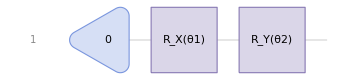

```mathematica
V=QuantumCircuitOperator[{"0","RX"[θ1]->{1},"RY"[θ2]->{1}},"Parameters"->{θ1,θ2}];
"Diagram"//V
```

Calculate ϕ (θ) from the ansatz circuit V:

```mathematica
ϕ=V[];
"Formula"//ϕ
```

(Cos[θ1/2] Cos[θ2/2]+ⅈ Sin[θ1/2] Sin[θ2/2])0+(-ⅈ Cos[θ2/2] Sin[θ1/2]+Cos[θ1/2] Sin[θ2/2])1

Implement the cost function ℒ as stated before:

```mathematica
ℒ[θ1_,θ2_]=ComplexExpand["Scalar"//SuperDagger[ϕ]@H@ϕ];
ℒ[θ1, θ2]//Simplify
```

Cos[θ1] (Cos[θ2]+Sin[θ2])

Calculate the ground state eigenvalue of H by minimizing 𝒻:

```mathematica
MinValue[ℒ[θ1, θ2], {θ1, θ2}]
```

-√2

### Visualizations

In order to visualize the optimization process, we need to get all the parameter values during the evolution, in this case we will use a simple gradient descent method:

```mathematica
initialPosition={0.1,0.1};
```

```mathematica
params=GradientDescent[ℒ,initialPosition];
```

It would be also useful to calculate all the cost function values during each step of the parameter evolution:

```mathematica
costs=ℒ@@@params;
```

#### Cost curve

We can visualize the evolution of our optimization during time in an Cost Curve, also known as Loss Curve:

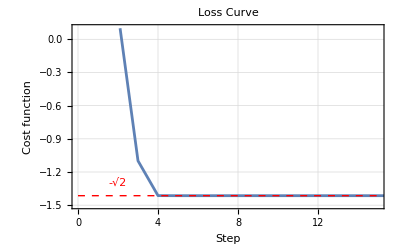

```mathematica
ListLinePlot[costs,PlotRange->{{0,15},{-1.5,0.1}},PlotLabel->"Loss Curve",Frame->True,GridLines->Automatic,FrameLabel->{"Step","Cost function"},ImageMargins->1,
Epilog->{{Red,Dashed,Line[{{0,-√2},{15,-√2}}]},{Red,Inset["-√2",{2,-1.3}]}}
]
```

#### Parameter Space

We can visualize the evolution of our optimization in the parameter space in a Contour Plot:

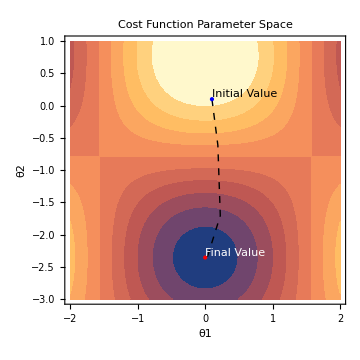

```mathematica
ContourPlot[ℒ[θ1,θ2],]
```

#### Gradient Vector Plot

The stream plot of the gradient of our cost function can provide insight into the behavior of the evolution as observed in its parameter space:

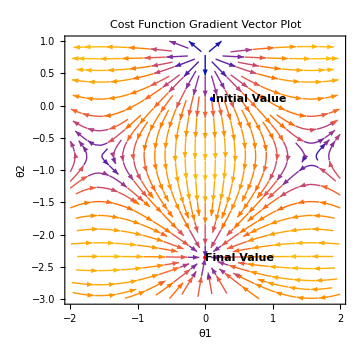

```mathematica
StreamPlot[Evaluate[-Grad[ℒ[θ1, θ2], {θ1, θ2}]],]
```

### Quantum Chemistry

The Variational Quantum Eigensolver (VQE) is a valuable tool in quantum chemistry for finding the minimal energy of a molecule. The task is essentially an optimization problem, where the goal is to minimize the total energy of the molecule with respect to the positions of the atomic nuclei.

In the case of VQE, we use parameterized quantum circuits to approximate the ground state energy of the system. This results in the determination of the minimal energy of the system, which corresponds to the lowest energy configuration of the molecule in its ground state.

This minimal energy result can be incredibly useful in determining the geometry of the molecule as well, as the lowest energy corresponds to the optimized configuration of the atomic nuclei. Therefore, although the main goal is to minimize the energy, this process can also provide insights into the stable arrangement of atoms in the molecule.

#### Toy H_2 Molecule

The current problem is finding the ground state of the H_2 molecule;,the Hamiltonian can be reduced and modeled using two qubits as:

```mathematica
H2=QuantumOperator[α("ZI"+"IZ")+β*"XX"]
```

QuantumOperator[…]

Implement the algorithm as we learned last class:

First: Parametrized quantum circuits, state and ansatz preparation.

In this case we will use a typical hardware-efficient ansatz: Two layers of Rotations and a CNOT to ensure the entanglement.

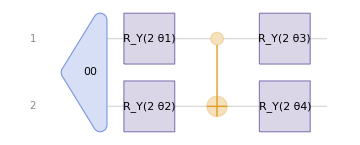

```mathematica
HEAnsatz=QuantumCircuitOperator[{"00","RY"[2 θ1]->1,"RY"[2 θ2]->2,"CNOT"->{1,2},"RY"[2 θ3]->1,"RY"[2 θ4]->2}];
HEAnsatz["Diagram"]
```

Second: Cost function ⟨ H (θ)  ⟩

We need a cost function, so let’s obtain the QuantumState from the QuantumCircuit and define the bra and ket.

```mathematica
ϕ=HEAnsatz[];ϕ=SuperDagger[ϕ];
```

Finally lets compute the energy of our system and define a function that will work as the cost function. In this step we should help the optimizer by Simplifying and replacing fixed values.

```mathematica
energy=ϕ@H2@ϕ ;
```

```mathematica
values={α->0.4,β->0.2};
costH2[θ1_,θ2_,θ3_,θ4_]=FullSimplify["Scalar"//energy,{θ1,θ2,θ3,θ4}∈Reals]/.values
```

Sin[2 θ1] (0.2 Cos[2 θ3] Cos[2 θ4]-0.4 Sin[2 θ2] Sin[2 θ3])+Cos[2 θ1] (0.4 Cos[2 θ3]+Cos[2 θ4] (0.4 Cos[2 θ2]+0.2 Sin[2 θ2] Sin[2 θ3]))+(-0.4 Sin[2 θ2]+0.2 Cos[2 θ2] Sin[2 θ3]) Sin[2 θ4]

As I mentioned, the cost function we are working with is not trivial, but the advantage is that we can compute it symbolically, which significantly helps in the optimization process.

Third: Optimization

To find the optimal parameters for our quantum circuit, we can use the NMinimize function in Mathematica.

```mathematica
resultH2=NMinimize[costH2[θ1,θ2,θ3,θ4],{θ1,θ2,θ3,θ4}]
```

{-0.824621,{θ1→0.717444,θ2→-0.909051,θ3→-0.855457,θ4→2.37329}}

This function allows us to minimize the cost function by adjusting the parameters, and after performing this minimization, we obtain the optimized parameters and the minimum value of the cost function, which in this case is approximately -0.824.

```mathematica
paramH2=Last[resultH2]//Association
```

<|θ1→0.717444,θ2→-0.909051,θ3→-0.855457,θ4→2.37329|>

Now that we have the optimal value, it is insightful to inspect the behavior of the cost function around these points. Since we have four variables (the parameters in the ansatz), we need to fix two of the values in order to visualize the function.

We can do this by using a ContourPlot, which will allow us to observe the shape of the cost function in two dimensions.

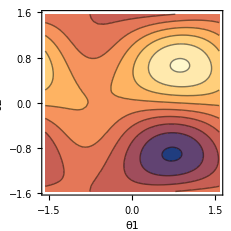

```mathematica
ContourPlot[costH2[θ1,θ2,paramH2[θ3],paramH2[θ4]],{θ1,-π/2,π/2},{θ2,-π/2,π/2},FrameLabel->Automatic]
```

ContourPlot is useful because it highlights where the cost function attains higher and lower values. In this plot, the lighter sections correspond to higher values, and the blue sections represent the lowest values of the cost function.

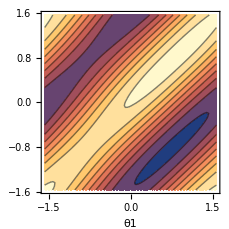

```mathematica
ContourPlot[costH2[θ1,paramH2[θ2],θ3,paramH2[θ4]],{θ1,-π/2,π/2},{θ3,-π/2,π/2},FrameLabel->Automatic]
```

If the optimization algorithm has started with a point near the blue section (where the minimum lies), we can expect it to converge towards this blue region, as this represents the optimal set of parameters. The algorithm searches for regions where the cost is minimized, and this plot helps visualize the “shape” of the function.

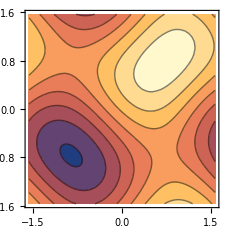

```mathematica
ContourPlot[costH2[paramH2[θ1],paramH2[θ2],θ3,θ4],{θ3,-π/2,π/2},{θ4,-π/2,π/2}]
```

When the cost function is relatively simple and can be expressed symbolically, the ContourPlot can exhibit repetitive patterns. This repetition often results from the periodic nature of trigonometric functions (e.g., sin⁡and cos) that may appear in the cost function due to the rotation gates used in the ansatz.

Example from  https://arxiv.org/pdf/1909.05074v1

#### Trihydrogen cation

In this example we will obtain the minimal energy for the molecule Cation H_3^+.

First we will use some python code from PennyLane to obtain the Hamiltonian corresponding to the H3 cation.

We just need to indicate the molecules “H” and the coordinates:

import pennylane as qml
from pennylane import numpy as np

symbols = ["H", "H", "H"]
coordinates = np.array([0.028, 0.054, 0.0, 0.986, 1.610, 0.0, 1.855, 0.002, 0.0])

# Building the molecular hamiltonian for the trihydrogen cation
hamiltonian, qubits = qml.qchem.molecular_hamiltonian(symbols, coordinates, charge=1)

qml.matrix(hamiltonian)

NumericArray[…]

In case Python is not available, you can import it from this location:

```mathematica
Import["https://wolfr.am/1uXbew3vg"]
```

NumericArray[…]

Finally we obtain a NumericArray which we will turn into a QuantumOperator:

```mathematica
H3=QuantumOperator[%//Normal]
```

QuantumOperator[…]

If we have no prior knowledge of the structure of the circuit, a reasonable starting point could be a layered circuit consisting of rotations around the Y-axis and CNOT gates.

To encode the occupation numbers of the molecular spin-orbitals, we would need six qubits.

```mathematica
param=GenerateParameters[6,2];
basicMixAnsatz=QuantumCircuitOperator[{
ParametrizedLayer["RY",Range[1,6]],
EntanglementLayer["CNOT",Range[6]],
"Barrier",
ParametrizedLayer["RY",Range[7,12]]
},
"Parameters"->param
];
```

If you’d like to learn how to construct layered circuits using ParametrizedLayer and EntanglementLayer please refer to the Quantum Optimization documentation.

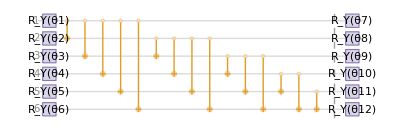

```mathematica
basicMixAnsatz["Diagram",ImageSize->Full]
```

In this case, you can expect a very complex symbolic cost function. To handle this, we could choose to implement a numerical function instead.

```mathematica
stateAnsatz=basicMixAnsatz[];
```

```mathematica
matrixH3=H3["Matrix"];
```

We begin by using Module to define the quantum state with parameters replaced by real numbers.  Next, we define the ket and bra, and then compute the scalar resulting from the expectation value of the Hamiltonian H.

```mathematica
ClearAll[meanEnergy]
meanEnergy[values_,H_]:=Module[{ket,bra,state},
state=stateAnsatz[AssociationThread[param,values]];
ket=state["StateVector"];
bra=SuperDagger[state]["StateVector"];
Re[bra.H.ket]
]
```

After defining the cost function, we can apply a classical optimizer starting from an initial guess to find the minimum energy value.

```mathematica
init=Thread[{param,{π,0,0,0,π/2,π,0,0,0,0,π,0}}];
```

```mathematica
FindMinimum[meanEnergy[param,matrixH3],init]//Quiet
```

{-1.30949,{θ1→3.13598,θ2→-0.196715,θ3→-0.00696906,θ4→-0.00209702,θ5→1.45483,θ6→3.14184,θ7→-3.02125×10^-7,θ8→-2.94889×10^-7,θ9→2.37779×10^-7,θ10→-8.8975×10^-7,θ11→3.14373,θ12→-3.14374}}

If we are interested in obtaining the geometry of the system, we would need to introduce a parameterized Hamiltonian for optimization as well, to optimize both the energy and the geometry.

Exercises

The following code in Python calculates the Hamiltonian for the H_2 molecule. Calculate the minimal energy . (You can import the Hamiltonian from the following link: Import["https://wolfr.am/1tP2IKEfw"])

```mathematica
import pennylane as qml
from pennylane import numpy as np

symbols = ["H", "H"]
coordinates = np.array([[0.0, 0.0, -0.6614], [0.0, 0.0, 0.6614]])

# Building the molecular hamiltonian 
hamiltonian, qubits = qml.qchem.molecular_hamiltonian(symbols, coordinates)

qml.matrix(hamiltonian)
```